# Test and Filter Runs

n: number of stars
NS: number of simulations
R: virial radius
Isolated System

### Logs

```mathematica
Print[$RunNumber]
```

600

```mathematica
Print[script`path]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest

```mathematica
logstream = OpenWrite[
FileNameJoin[{script`path, "nbstatus" <> ToString[$RunNumber] <> ".log"}],
FormatType->OutputForm
]
```

OutputStream[…]

```mathematica
Write[logstream, "Begin log ...."];
```

## Initialization

```mathematica
{$MachineName,$Version}
```

{tars,12.1.0 for Linux x86 (64-bit) (March 18, 2020)}

```mathematica
AppendTo[$Path,Environment["MYGITDIR"]];
```

```mathematica
Get["AstroTools`nbody6`"]
```

```mathematica
Get["AstroTools`Utilities`"]
```

```mathematica
$ConfiguredKernels = 
 List[SubKernels`LocalKernels`LocalMachine[30, 
   Rule[SubKernels`LocalKernels`LowerPriority, True]]]
```

{SubKernels`LocalKernels`LocalMachine[30,SubKernels`LocalKernels`LowerPriority→True]}

```mathematica
$SAVEMXQ=False
```

False

```mathematica
resultsPath=FileNameJoin[{Environment["MYGITDIR"],"workspace","nbody6","isolated","n"<>ToString[$RunNumber],"NSX-R1","results"}]
```

/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results

```mathematica
SetDirectory[resultsPath]
```

/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results

```mathematica
FileNames[]
```

{run-1,run-10,run-100,run-101,run-102,run-103,run-104,run-105,run-106,run-107,run-108,run-109,run-11,run-110,run-111,run-112,run-113,run-114,run-115,run-116,run-117,run-118,run-119,run-12,run-120,run-121,run-122,run-123,run-124,run-125,run-126,run-127,run-128,run-129,run-13,run-130,run-131,run-132,run-133,run-134,run-135,run-136,run-137,run-138,run-139,run-14,run-140,run-141,run-142,run-143,run-144,run-145,run-146,run-147,run-148,run-149,run-15,run-150,run-151,run-152,run-153,run-154,run-155,run-156,run-157,run-158,run-159,run-16,run-160,run-161,run-162,run-163,run-164,run-165,run-166,run-167,run-168,run-169,run-17,run-170,run-171,run-172,run-173,run-174,run-175,run-176,run-177,run-178,run-179,run-18,run-180,run-181,run-182,run-183,run-184,run-185,run-186,run-187,run-188,run-189,run-19,run-190,run-191,run-192,run-193,run-194,run-195,run-196,run-197,run-198,run-199,run-2,run-20,run-200,run-201,run-202,run-203,run-204,run-205,run-206,run-207,run-208,run-209,run-21,run-210,run-211,run-212,run-213,run-214,run-215,run-216,run-217,run-218,run-219,run-22,run-220,run-221,run-222,run-223,run-224,run-225,run-226,run-227,run-228,run-229,run-23,run-230,run-231,run-232,run-233,run-234,run-235,run-236,run-237,run-238,run-239,run-24,run-240,run-241,run-242,run-243,run-244,run-245,run-246,run-247,run-248,run-249,run-25,run-250,run-251,run-252,run-253,run-254,run-255,run-256,run-257,run-258,run-259,run-26,run-260,run-261,run-262,run-263,run-264,run-265,run-266,run-267,run-268,run-269,run-27,run-270,run-271,run-272,run-273,run-274,run-275,run-276,run-277,run-278,run-279,run-28,run-280,run-281,run-282,run-283,run-284,run-285,run-286,run-287,run-288,run-289,run-29,run-290,run-291,run-292,run-293,run-294,run-295,run-296,run-297,run-298,run-299,run-3,run-30,run-300,run-301,run-302,run-303,run-304,run-305,run-306,run-307,run-308,run-309,run-31,run-310,run-311,run-312,run-313,run-314,run-315,run-316,run-317,run-318,run-319,run-32,run-320,run-321,run-322,run-323,run-324,run-325,run-326,run-327,run-328,run-329,run-33,run-330,run-331,run-332,run-333,run-334,run-335,run-336,run-337,run-338,run-339,run-34,run-340,run-341,run-342,run-343,run-344,run-345,run-346,run-347,run-348,run-349,run-35,run-350,run-351,run-352,run-353,run-354,run-355,run-356,run-357,run-358,run-359,run-36,run-360,run-361,run-362,run-363,run-364,run-365,run-366,run-367,run-368,run-369,run-37,run-370,run-371,run-372,run-373,run-374,run-375,run-376,run-377,run-378,run-379,run-38,run-380,run-381,run-382,run-383,run-384,run-385,run-386,run-387,run-388,run-389,run-39,run-390,run-391,run-392,run-393,run-394,run-395,run-396,run-397,run-398,run-399,run-4,run-40,run-400,run-401,run-402,run-403,run-404,run-405,run-406,run-407,run-408,run-409,run-41,run-410,run-411,run-412,run-413,run-414,run-415,run-416,run-417,run-418,run-419,run-42,run-420,run-421,run-422,run-423,run-424,run-425,run-426,run-427,run-428,run-429,run-43,run-430,run-431,run-432,run-433,run-434,run-435,run-436,run-437,run-438,run-439,run-44,run-440,run-441,run-442,run-443,run-444,run-445,run-446,run-447,run-448,run-449,run-45,run-450,run-46,run-47,run-48,run-49,run-5,run-50,run-51,run-52,run-53,run-54,run-55,run-56,run-57,run-58,run-59,run-6,run-60,run-61,run-62,run-63,run-64,run-65,run-66,run-67,run-68,run-69,run-7,run-70,run-71,run-72,run-73,run-74,run-75,run-76,run-77,run-78,run-79,run-8,run-80,run-81,run-82,run-83,run-84,run-85,run-86,run-87,run-88,run-89,run-9,run-90,run-91,run-92,run-93,run-94,run-95,run-96,run-97,run-98,run-99}

## Delete invalid runs

```mathematica
If[Not[DirectoryQ["temp"]],
Import["!../run2end.sh","String"];goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];dirs=DirectoryName/@goodFiles;dirsToDelete=Complement[Select[FileNames[],DirectoryQ],Part[StringSplit[#,$PathnameSeparator]&/@dirs,All,2]];dirsToDelete=Flatten[StringCases[dirsToDelete,"run-"~~__]];Print[dirsToDelete//Short];Print[dirsToDelete//Length];(*Table[Style[Import[StringTemplate["!tail -n 2 ``/output"][dirsToDelete[[j]]],"String"],If[OddQ[j],Blue,Brown]],{j,Length@dirsToDelete}]//ColumnForm*)
If[Length[dirsToDelete]≠0,
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete,
Print["Nothing to delete"]];
CreateDirectory["temp"];
runsToMove=FileNames["run*"];
CopyFile[#,"./temp/"<>FileBaseName[#]]&/@runsToMove;DeleteDirectory[#,DeleteContents->True]&/@runsToMove;DeleteFile["goodRuns.log"];
]
```

{run-1,run-101,run-102,run-103,run-104,run-106,run-107,run-108,run-110,run-113,run-115,run-116,run-117,run-118,run-119,run-12,run-120,run-121,run-123,run-125,run-126,run-127,run-128,run-129,run-13,run-131,run-132,run-133,run-134,run-137,run-138,run-139,run-14,run-140,run-141,run-142,run-143,run-144,run-145,run-146,run-148,run-149,run-15,run-150,run-152,run-154,run-155,run-157,run-16,run-162,run-163,run-164,run-167,run-168,run-169,run-17,run-170,run-171,run-172,run-174,run-175,run-176,run-177,run-178,run-179,run-18,run-181,run-182,run-183,run-184,run-185,run-186,run-187,run-189,run-19,run-191,run-192,run-194,run-196,run-197,run-198,run-199,run-200,run-202,run-204,run-206,run-207,run-209,run-210,run-213,run-214,run-215,run-216,run-217,run-218,run-22,run-220,run-221,run-223,run-224,run-225,run-226,run-227,run-228,run-23,run-230,run-232,run-233,run-235,run-236,run-237,run-238,run-239,run-24,run-241,run-243,run-244,run-246,run-247,run-248,run-249,run-25,run-250,run-251,run-255,run-256,run-257,run-258,run-259,run-260,run-261,run-262,run-263,run-265,run-266,run-267,run-268,run-270,run-272,run-274,run-275,run-278,run-279,run-282,run-283,run-284,run-285,run-288,run-289,run-29,run-290,run-291,run-292,run-295,run-296,run-297,run-298,run-299,run-3,run-30,run-301,run-302,run-303,run-305,run-307,run-308,run-309,run-31,run-311,run-312,run-314,run-315,run-317,run-318,run-32,run-320,run-321,run-322,run-323,run-324,run-327,run-329,run-33,run-331,run-332,run-333,run-334,run-335,run-336,run-337,run-338,run-339,run-34,run-340,run-341,run-342,run-343,run-345,run-346,run-347,run-348,run-349,run-35,run-350,run-353,run-354,run-355,run-357,run-359,run-36,run-363,run-364,run-366,run-367,run-369,run-370,run-371,run-372,run-373,run-375,run-377,run-382,run-383,run-384,run-385,run-386,run-387,run-389,run-39,run-390,run-392,run-393,run-394,run-395,run-398,run-399,run-40,run-400,run-401,run-402,run-403,run-404,run-405,run-406,run-407,run-408,run-409,run-410,run-411,run-412,run-413,run-414,run-415,run-416,run-417,run-418,run-42,run-421,run-422,run-423,run-424,run-427,run-43,run-431,run-432,run-433,run-434,run-435,run-436,run-437,run-438,run-44,run-440,run-441,run-443,run-444,run-445,run-449,run-45,run-450,run-47,run-50,run-51,run-54,run-55,run-56,run-61,run-62,run-64,run-65,run-66,run-67,run-7,run-71,run-72,run-73,run-78,run-79,run-81,run-82,run-84,run-86,run-88,run-90,run-91,run-92,run-93,run-94,run-95,run-96,run-97,run-99}

312

```mathematica
Write[logstream, "goo shape run directories moved to temp"]
```

### MOVE runs from TEMP

```mathematica
(**** IMPORTANT: run this section only in ByGroup mode ****)
```

```mathematica
filesToMove=Take[FileNames["temp/run*"],UpTo[50]]
```

{temp/run-10,temp/run-100,temp/run-105,temp/run-109,temp/run-11,temp/run-111,temp/run-112,temp/run-114,temp/run-122,temp/run-124,temp/run-130,temp/run-135,temp/run-136,temp/run-147,temp/run-151,temp/run-153,temp/run-156,temp/run-158,temp/run-159,temp/run-160,temp/run-161,temp/run-165,temp/run-166,temp/run-173,temp/run-180,temp/run-188,temp/run-190,temp/run-193,temp/run-195,temp/run-2,temp/run-20,temp/run-201,temp/run-203,temp/run-205,temp/run-208,temp/run-21,temp/run-211,temp/run-212,temp/run-219,temp/run-222,temp/run-229,temp/run-231,temp/run-234,temp/run-240,temp/run-242,temp/run-245,temp/run-252,temp/run-253,temp/run-254,temp/run-26}

```mathematica
If[filesToMove==={},
goodRuns=Take[FileNames["good-runs/run*"],UpTo[50]];
Print@Length[goodRuns];badRuns=Take[FileNames["bad-runs/run*"],UpTo[Max[0,50-Length[goodRuns]]]];Print@Length[badRuns];CopyFile[#,"./"<>FileBaseName[#]]&/@Join[goodRuns,badRuns];DeleteDirectory[#,DeleteContents->True]&/@Join[goodRuns,badRuns];Import["!../run2end.sh","String"];
Quit[]
]
```

```mathematica
CopyFile[#,"./"<>FileBaseName[#]]&/@filesToMove
```

{/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-10,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-100,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-105,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-109,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-11,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-111,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-112,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-114,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-122,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-124,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-130,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-135,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-136,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-147,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-151,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-153,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-156,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-158,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-159,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-160,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-161,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-165,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-166,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-173,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-180,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-188,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-190,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-193,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-195,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-2,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-20,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-201,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-203,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-205,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-208,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-21,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-211,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-212,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-219,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-222,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-229,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-231,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-234,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-240,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-242,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-245,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-252,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-253,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-254,/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results/run-26}

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@filesToMove
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Import["!../run2end.sh","String"]
```

```mathematica
Write[logstream, "moved upt to 50 files to proccess"]
```

### n–body parameters

```mathematica
(*
numberOfStars=380;
nb["S0"]=0.3(numberOfStars/1000)^(1/3)
nb["nMAX"]=2.(numberOfStars)^(1/2)
*)
```

```mathematica
FilePrint["../create-ini.sh"]
```

#!/bin/bash

echo "[`date`] Start"

mkdir ./results/

cd results/
for filenumber in {1..450..1}
do
	mkdir "./run-$filenumber/"
  	cat << EOF > ./run-$filenumber/ini.dat
1 20.0
600 1 10 $RANDOM 53 1
0.02 0.01 0.25 2.0 2.0 3000.0 1.0E-03 1 0.5
0 0 1 0 1 0 0 0 0 0
0 0 0 0 0 0 0 0 0 6
0 0 0 0 0 0 0 0 0 0
0 0 0 0 0 0 0 0 0 1
0 0 0 0 0 0 0 0 0 0
2.0E-05 0.001 0.2 1.0 1.0E-06 0.001
2.3 50.0 0.2 0 0 0.002 0 0
0.5 0 0 0 0.5
EOF

done

cd ..
echo `pwd`
echo "[`date`] End"
echo "time elapsed: $SECONDS"
echo all done

```mathematica
strCreateFile=Import["../create-ini.sh","Table"]
```

{{#!/bin/bash},{},{echo,[`date`] Start},{},{mkdir,./results/},{},{cd,results/},{for,filenumber,in,{1..450..1}},{do},{mkdir,./run-$filenumber/},{cat,<<,EOF,>,./run-$filenumber/ini.dat},{1,20.},{600,1,10,$RANDOM,53,1},{0.02,0.01,0.25,2.,2.,3000.,0.001,1,0.5},{0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,6},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0.00002,0.001,0.2,1.,1.×10^-6,0.001},{2.3,50.,0.2,0,0,0.002,0,0},{0.5,0,0,0,0.5},{EOF},{},{done},{},{cd,..},{echo,`pwd`},{echo,[`date`] End},{echo,time elapsed: $SECONDS},{echo,all,done},{},{}}

```mathematica
pos=Position[strCreateFile,"$RANDOM"][[1,1]];
numberOfStars=strCreateFile[[pos,1]]
nbodyStep=Floor@(strCreateFile[[pos+1,5]])
maxNbodyTime=Floor@(strCreateFile[[pos+1,6]]-nbodyStep)
```

600

2

2998

### Other global variables

#### Data

```mathematica
goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];
```

```mathematica
dirs=DirectoryName/@goodFiles;
```

```mathematica
runmax=Length[dirs]
```

50

```mathematica
If[!FileExistsQ["nbody6-data.mx"]
,
Print["Loading from source ..."];
data=ReadOutput/@goodFiles;
If[$SAVEMXQ,DumpSave["nbody6-data.mx",data]];
,
Print["Loading from MX ..."];
Get["nbody6-data.mx"];
]//AbsoluteTiming
```

Loading from source ...

ReadList::readn: Invalid real number found when reading from «1».

General::stop: Further output of «1» will be suppressed during this calculation.

{21.1811,Null}

```mathematica
parameters=data[[All,1]];
```

```mathematica
parameters//Length
```

50

```mathematica
data=data[[All,2]];
```

```mathematica
lengthOfRuns=Tally[Length/@data]
```

{{1500,50}}

#### Parameters

```mathematica
(* NOTE 1: parameters V^*, T^*, M^* are different for each run *)
(* NOTE 2: $MeanMass numberOfStats ≈ $MassScale *)
parameters[[All,4]]
```

{0.668,0.65,0.704,0.657,0.598,0.729,0.69,0.651,0.652,0.614,0.652,0.593,0.677,0.662,0.64,0.684,0.649,0.64,0.619,0.634,0.667,0.725,0.725,0.654,0.689,0.705,0.636,0.66,0.696,0.666,0.646,0.67,0.659,0.67,0.664,0.621,0.616,0.614,0.684,0.697,0.648,0.689,0.696,0.599,0.723,0.598,0.64,0.71,0.666,0.69}

```mathematica
{$LengthScale,$MassScale,$SpeedScale,$TimeScale,$MeanMass,$SU}=Mean[parameters]
```

{1.,511.888,1.48166,0.66172,0.8528,4.4×10^7}

```mathematica
$EnergyScale=$MassScale ($SpeedScale)^2
```

1123.76

```mathematica
$DensityScale=$MassScale/($LengthScale)^3
```

511.888

```mathematica
(* in units of Msun/pc^3*)
ρSunNeighborPhysical=0.09;
ρForClusterDisruptionPhysical=0.08;
```

```mathematica
(* in units of n-body units *)
ρSunNeighbor=ρSunNeighborPhysical/$DensityScale;
ρForClusterDisruption=ρForClusterDisruptionPhysical/$DensityScale;
```

```mathematica
(* checking units *)
ρSunNeighbor
```

0.00017582

```mathematica
(* mean density in nbody units *)
$MeanDensity=1./(4/3Pi(1)^3)
```

0.238732

```mathematica
(* mean density physical Msun/pc^3 *)
$MeanDensity $DensityScale
```

122.204

```mathematica
(* Max elpased time for evolution in MY*)
maxNbodyTime*$TimeScale
```

1983.84

```mathematica
(* INITIAL TIME = 0 -> following nbody6 *)
timeArray=Range[0,maxNbodyTime,nbodyStep];
(* log step array: 0 time at -1 *)
log10TimeArray1=N@Prepend[Log10[Rest[timeArray]],0];
log10TimeArrayScaled1=N@Prepend[Log10[Rest[$TimeScale timeArray]],0];
```

```mathematica
Length/@{timeArray,log10TimeArray1,log10TimeArrayScaled1}
```

{1500,1500,1500}

## run cpu timings

```mathematica
Directory[]
```

/home/cesarg/git/workspace/nbody6/isolated/n600/NSX-R1/results

```mathematica
timingFiles=FileNames["run*/timings"];
timingFiles//Short
```

{run-100/timings,run-105/timings,run-109/timings,run-10/timings,run-111/timings,run-112/timings,run-114/timings,run-11/timings,run-122/timings,run-124/timings,run-130/timings,run-135/timings,run-136/timings,run-147/timings,run-151/timings,run-153/timings,run-156/timings,run-158/timings,run-159/timings,run-160/timings,run-161/timings,run-165/timings,run-166/timings,run-173/timings,run-180/timings,run-188/timings,run-190/timings,run-193/timings,run-195/timings,run-201/timings,run-203/timings,run-205/timings,run-208/timings,run-20/timings,run-211/timings,run-212/timings,run-219/timings,run-21/timings,run-222/timings,run-229/timings,run-231/timings,run-234/timings,run-240/timings,run-242/timings,run-245/timings,run-252/timings,run-253/timings,run-254/timings,run-26/timings,run-2/timings}

```mathematica
timeStrings=Cases[Import[#],{"real",_}][[1,2]]&/@timingFiles;
timeStrings//Short
```

{2m21.230s,3m3.662s,2m6.225s,2m18.395s,1m34.956s,2m7.128s,2m48.268s,1m53.859s,3m15.735s,3m16.384s,1m55.127s,2m31.762s,2m39.257s,3m20.448s,1m29.924s,2m57.927s,3m24.601s,2m15.722s,2m11.154s,2m55.747s,1m59.263s,2m29.920s,5m24.660s,3m30.846s,2m26.281s,3m1.276s,1m31.594s,4m20.631s,2m34.191s,1m41.572s,2m4.781s,2m43.810s,3m0.371s,2m17.787s,2m37.883s,3m13.804s,1m45.874s,2m57.926s,2m7.409s,2m13.310s,2m53.116s,1m40.791s,2m22.679s,1m30.136s,1m56.390s,1m57.387s,2m15.954s,2m35.892s,2m49.979s,2m18.863s}

```mathematica
timeElapsedStringToSeconds[string_]:=(60#1+#2)&@@ToExpression[StringSplit[string,"m"|"s"]]
```

```mathematica
timings=timeElapsedStringToSeconds/@timeStrings;
```

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@Mean[timings]
```

Set::write: Tag «12» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

SetDelayed::write: Tag «11» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

2.5373 min

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@StandardDeviation[timings]
```

43.9464 s

## n–body results

### Mean rhalf

```mathematica
meanRhalf=Mean/@DeleteCases[Transpose[data[[All,All,1]]],$Failed,{2}];
```

```mathematica
meanRhalfAndTime=Transpose[{timeArray,meanRhalf}];
```

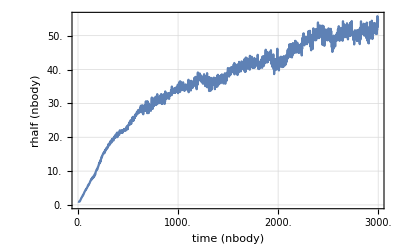

```mathematica
meanRhalfAndTimePlot=ScaledListPlot[meanRhalfAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rhalf (nbody)","rhalf (pc)"},{"time (nbody)","time (My)"}},
"ShowAllScales"->True]
```

### Mean rdens

```mathematica
meanRdens=Mean/@DeleteCases[Transpose[data[[All,All,3]]],$Failed,{2}];
```

```mathematica
meanRdensAndTime=Transpose[{timeArray,meanRdens}];
```

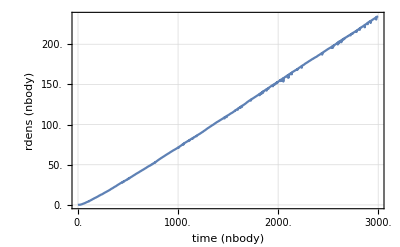

```mathematica
meanRdensAndTimePlot=ScaledListPlot[meanRdensAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rdens (nbody)","rdens (pc)"},{"time (nbody)","time (My)"}},"ShowAllScales"->True]
```

## Loading Data

#### Load from OUT3 or MX

```mathematica
(* 8 values: id, pos, vel, mass *)
(* 8 bytes each one *)
```

```mathematica
(numberOfStars*maxNbodyTime*runmax*8*8)/(1024*1024*1024. nbodyStep)
```

2.68042

```mathematica
snapshots=All;
```

```mathematica
(*snapshots=Range[1,maxNbodyTime,10];*)
```

```mathematica
Write[logstream, "computing particles.mx ...."]
```

```mathematica
(* Check also: "particles.bin" *)
If[!FileExistsQ["particles.mx"]
	,
	Print[TimeAndMem[]];
	(*While[Kernels[] == {}, 
		kernels = LaunchKernels[];
		];*)
	kernels = LaunchKernels[];
	Write[logstream, kernels];
	Print["Kernels: ", kernels];
	SetSharedVariable[dirs];
	ParallelEvaluate[AppendTo[$Path, Environment["MYGITDIR"]]];
	ParallelEvaluate[SetDirectory[resultsPath]];
	ParallelNeeds["AstroTools`nbody6`"];
	ParallelNeeds["AstroTools`Utilities`"];
	(particles = 
		Transpose@
		ParallelTable[
			SetDirectory[dirs[[i]]];
			Print["DIR: ", dirs[[i]]];
			{bodys,xs,vs,name} = Flatten[ReadOUT3["OUT3","Snapshots" -> snapshots], 1];
			xs=Partition[#,3]&/@xs;
			vs=Partition[#,3]&/@vs;
			ResetDirectory[]; 
			{bodys,xs,vs,name}
			,
			{i,1,Length[dirs]}]);
	
	Print["Closing kernels ..."];
	CloseKernels[];

	(*-- SAVE to a MX file --*)
	If[$SAVEMXQ,
		Print["Saving data to MX ... "];
		Print[TimeAndMem[]];
		DumpSave["particles.mx", particles];
		Print[TimeAndMem[]];
	];

	(*-- SAVE to a BIN file --*)
	(* BinarySerializeSave[particles,"particles.bin"]; // AbsoluteTiming *)
	
	,
	
	(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["particles.mx"];
] // AbsoluteTiming
```

14:54:36 mem:180.434MB

Kernels: {KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

DIR: ./run-100/

DIR: ./run-109/

DIR: ./run-111/

DIR: ./run-114/

DIR: ./run-122/

DIR: ./run-130/

DIR: ./run-136/

DIR: ./run-151/

DIR: ./run-156/

DIR: ./run-159/

DIR: ./run-161/

DIR: ./run-166/

DIR: ./run-180/

DIR: ./run-190/

DIR: ./run-195/

DIR: ./run-203/

DIR: ./run-208/

DIR: ./run-211/

DIR: ./run-219/

DIR: ./run-222/

DIR: ./run-231/

DIR: ./run-234/

DIR: ./run-240/

DIR: ./run-242/

DIR: ./run-245/

DIR: ./run-252/

DIR: ./run-253/

DIR: ./run-254/

DIR: ./run-26/

DIR: ./run-2/

DIR: ./run-112/

DIR: ./run-173/

DIR: ./run-212/

DIR: ./run-21/

DIR: ./run-105/

DIR: ./run-10/

DIR: ./run-11/

DIR: ./run-124/

DIR: ./run-135/

DIR: ./run-147/

DIR: ./run-153/

DIR: ./run-158/

DIR: ./run-160/

DIR: ./run-165/

DIR: ./run-188/

DIR: ./run-193/

DIR: ./run-201/

DIR: ./run-205/

DIR: ./run-20/

DIR: ./run-229/

Closing kernels ...

{237.246,Null}

```mathematica
Write[logstream, "particles.mx done!"]
```

```mathematica
(* --- serial computation ---
(particles=
Transpose@
Table[SetDirectory[dirs[[i]]];
Print["DIR: ", dirs[[i]]];
{bodys,xs,vs,name}=Flatten[ReadOUT3["OUT3","Snapshots"->All],1];
xs=Partition[#,3]&/@xs;
vs=Partition[#,3]&/@vs;
ResetDirectory[]; 
{bodys,xs,vs,name}
,{i,1,Length[dirs]}]);//AbsoluteTiming *)
```

#### Mem information

```mathematica
TimeAndMem[]
```

14:58:33 mem:11.632GB

```mathematica
(*PrintArrayInfo[particles]*)
```

```mathematica
DeleteOuts[500]
```

session mem: 11.632GB

No Out[] greater than 500MB

```mathematica
$numberOfRunsStatus=Dimensions[particles][[2]]
```

50

## Filtering Invalid Data

### Indexes To Extract Data

```mathematica
nbIndexes=Table[Range[maxNbodyTime/nbodyStep+1],{runmax}];
```

```mathematica
nbIndexes//Dimensions
```

{50,1500}

```mathematica
nbIndexes[[1]]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500}

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500}

### Incomplete runs

```mathematica
particles//Dimensions
```

{4,50,1500}

```mathematica
Length/@particles[[4]]//Union
```

{1500}

```mathematica
(* delete runs that have not complete data *)
maxtimes=Length/@particles[[4]]
```

{1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500}

```mathematica
delPos1=Position[maxtimes,x_/;x<Max[maxtimes]]
```

{}

```mathematica
delPos1//Length
```

0

#### FIX: Delete complete runs

```mathematica
Extract[dirs,delPos1]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos1],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete
```

{}

Opt – Update variables to continue computing

```mathematica
particles//Dimensions
```

{4,50,1500}

```mathematica
dirs=Delete[dirs,delPos1];
runmax=Length[dirs];
particles=Delete[#, delPos1]&/@particles;
nbIndexes=Delete[nbIndexes, delPos1];
nbLenIndexes=Length/@nbIndexes;
parameters=Delete[parameters, delPos1];
```

```mathematica
particles//Dimensions
```

{4,50,1500}

```mathematica
nbIndexes//Length
```

50

```mathematica
parameters//Dimensions
```

{50,6}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 12.1147GB

### Particles in the same position

#### TEST

```mathematica
particles[[All,All,All,1;;numberOfStars]]//Dimensions
```

{4,50,1500,600}

```mathematica
Clear[ceros];
If[!FileExistsQ["ceros.mx"],
ceros=Reap[
Do[
Print["run: ", run];
Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}];Print["CERO AT: ", run];Break[]]
]
,{t,1,nbLenIndexes[[run]]}
],
{run,1,runmax}]
];
DumpSave["ceros.mx", ceros]
,
(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["ceros.mx"];
];//AbsoluteTiming
```

run: 1

run: 2

run: 3

run: 4

run: 5

run: 6

run: 7

run: 8

run: 9

run: 10

run: 11

run: 12

run: 13

run: 14

run: 15

run: 16

CERO AT: 16

run: 17

run: 18

run: 19

run: 20

run: 21

run: 22

run: 23

run: 24

run: 25

run: 26

run: 27

run: 28

run: 29

run: 30

run: 31

run: 32

run: 33

run: 34

run: 35

run: 36

run: 37

run: 38

run: 39

run: 40

run: 41

run: 42

run: 43

run: 44

run: 45

run: 46

run: 47

run: 48

run: 49

run: 50

{1912.51,Null}

```mathematica
ceros[[2]]
```

{{{16,604}}}

#### Double check

```mathematica
(*invalid=With[{run=7},Reap[Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}]]
]
,{t,1,nbLenIndexes[[run]]}
]]
];*)
```

```mathematica
(*invalid//Short*)
```

```mathematica
(*With[{run=7, time=1100},
Select[GatherBy[Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}],Last],Length[#]>1&]]*)
```

```mathematica
(*With[
{part1=2,
part2=1,
run=46,
interTime=220
},
vel=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[3,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];
pos=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];

{ListLinePlot[{Norm/@vel[[All,1]],Norm/@vel[[All,2]]},
PlotRange->{{0,1000},{0,100}}],
ListLinePlot[{Norm/@pos[[All,1]],Norm/@pos[[All,2]]},
PlotRange->{{0,1000},{0,50000}},Epilog->InfiniteLine[{{interTime,0},{interTime,1}}]]}
]*)
```

```mathematica
(* testing indexes outside particles range *)
```

```mathematica
(*testing1001=Table[#[1001]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*Position[testimg1001,_Missing]*)
```

```mathematica
(*testing1002=Table[#[1002]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*testing1002[[8]]*)
```

#### FIX 1: Delete complete runs

```mathematica
delPos2=If[ceros[[2]]=={},{},Partition[Union[ceros[[2,1]][[All,1]]],1]];
```

```mathematica
delPos2//Short
```

{{16}}

```mathematica
Extract[dirs,delPos2]
```

{./run-153/}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos2],All,2]
```

{run-153}

```mathematica
dirsToDelete//Length
```

1

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

(* 
	Si dirsToDelete≠0 borrar *.m *.mx 
	generar goodRuns.log y correr nb de nuevo.
*)

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos2];
```

```mathematica
runmax=Length[dirs]
```

49

```mathematica
particles//Dimensions
```

{4,50,1500}

```mathematica
particles=Delete[#, delPos2]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,49,1500}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 11.8708GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos2];
```

```mathematica
nbIndexes//Length
```

49

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500,1500}

```mathematica
parameters//Dimensions
```

{50,6}

```mathematica
parameters=Delete[parameters, delPos2];
```

```mathematica
parameters//Dimensions
```

{49,6}

#### FIX 2: Delete specific snapshots (ruled out)

```mathematica
(* We will delete data only for snapshots containg equal positions *)
```

delPos3 = ceros[[2, 1]]

particles = Delete[#, delPos3] & /@ particles;

timeIndexes[[1, 450]]

Complement[Range[1000], timeIndexes[[1]]]

timeIndexes = Delete[timeIndexes, delPos3];

Complement[Range[1000], timeIndexes[[1]]]

nbLenIndexes = Length /@ timeIndexes

### Particles with index 0 / position 0.

#### TEST

```mathematica
(* Delete time snaphots of incorrect data with ceros in the position vector. *)
(* Very strange issue from nbody *)
```

```mathematica
delPos4=Position[particles[[4]],0][[All,{1,2}]];
```

```mathematica
delPos4//Short
```

{{2,216},{2,504},{2,505},{2,506},{3,325},{4,40},{6,415},{6,432},{6,433},{6,671},{6,672},{6,673},{6,674},{6,675},{6,676},{6,677},{6,678},{6,679},{6,680},{6,681},{6,895},{6,896},{6,897},{6,898},{6,1153},{7,26},{9,252},{10,17},{11,31},{11,32},{11,43},{14,300},{14,454},{16,14},{16,72},{16,73},{16,74},{16,75},{16,76},{16,77},{16,78},{16,79},{16,80},{16,81},{16,82},{16,83},{16,84},{16,85},{16,86},{16,87},{16,89},{16,90},{16,91},{16,114},{16,170},{17,26},{18,37},{18,38},{19,113},{19,914},{19,915},{19,916},{19,917},{19,918},{19,919},{19,920},{19,921},{19,922},{19,923},{19,924},{19,925},{19,926},{19,927},{19,928},{19,929},{19,930},{19,931},{19,932},{19,933},{19,934},{19,935},{19,936},{19,937},{19,938},{19,939},{19,940},{19,941},{19,942},{19,943},{19,944},{19,945},{19,946},{19,947},{19,948},{19,949},{19,950},{19,951},{19,952},{19,953},{21,92},{22,477},{22,478},{22,479},{22,480},{22,481},{22,715},{22,716},{22,717},{22,718},{22,719},{22,720},{22,721},{22,722},{22,723},{22,724},{22,725},{22,726},{22,727},{22,728},{22,729},{22,730},{22,731},{22,732},{22,733},{22,734},{22,735},{22,736},{22,737},{22,738},{22,739},{22,740},{22,741},{22,742},{22,743},{22,744},{22,745},{22,746},{22,747},{22,748},{22,749},{22,750},{22,751},{22,752},{22,753},{22,754},{22,755},{22,756},{22,757},{22,758},{22,759},{22,760},{22,761},{22,762},{22,763},{22,764},{22,765},{22,766},{22,767},{22,768},{22,769},{22,770},{22,771},{22,772},{22,773},{22,774},{22,775},{22,776},{22,777},{22,778},{22,779},{22,780},{22,781},{22,782},{22,783},{22,784},{22,785},{22,786},{22,787},{22,788},{22,789},{22,790},{22,791},{22,792},{22,793},{22,794},{22,795},{22,796},{22,797},{22,798},{22,799},{22,800},{22,801},{22,802},{22,803},{22,804},{22,805},{22,806},{22,807},{22,808},{22,809},{22,810},{22,811},{22,812},{22,813},{22,814},{22,815},{22,816},{22,817},{22,818},{22,819},{22,820},{22,821},{22,822},{22,823},{22,824},{22,825},{22,826},{22,827},{22,828},{22,829},{22,830},{22,831},{22,832},{22,833},{22,834},{22,835},{22,836},{22,837},{22,838},{22,839},{22,840},{22,841},{22,842},{22,843},{22,844},{22,845},{22,846},{22,847},{22,848},{22,849},{22,850},{22,851},{22,852},{22,853},{22,854},{22,855},{22,856},{22,857},{22,858},{22,859},{22,860},{22,861},{22,862},{22,863},{22,864},{22,865},{22,866},{22,867},{22,868},{22,869},{22,870},{22,871},{22,872},{22,873},{22,874},{22,875},{22,876},{22,877},{22,878},{22,879},{22,880},{22,881},{22,882},{22,883},{22,884},{22,885},{22,886},{22,887},{22,888},{22,889},{22,890},{22,891},{22,892},{22,893},{22,894},{22,895},{22,896},{22,897},{22,898},{22,899},{22,900},{22,901},{22,902},{22,903},{22,904},{22,905},{22,906},{22,907},{22,908},{22,909},{22,910},{22,911},{22,912},{22,913},{22,914},{22,915},{22,916},{22,917},{22,918},{22,919},{22,920},{22,921},{22,922},{22,923},{22,924},{22,925},{22,926},{22,927},{22,928},{22,929},{22,930},{22,931},{22,932},{22,933},{22,934},{22,935},{22,936},{22,937},{22,938},{22,939},{22,940},{22,941},{22,942},{22,943},{22,944},{22,945},{22,946},{22,947},{22,948},{22,949},{22,950},{22,951},{22,952},{22,953},{22,954},{22,955},{22,956},{22,957},{22,958},{22,959},{22,960},{22,961},{22,962},{22,963},{22,964},{22,965},{22,966},{22,967},{22,968},{22,969},{22,970},{22,971},{22,972},{22,973},{22,974},{22,975},{22,976},{22,977},{22,978},{22,979},{22,980},{22,981},{22,982},{22,983},{22,984},{22,985},{22,986},{22,987},{22,988},{22,989},{22,990},{22,991},{22,992},{22,993},{22,994},{22,995},{22,996},{22,997},{22,998},{22,999},{22,1000},{22,1001},{22,1002},{22,1003},{22,1004},{22,1005},{22,1006},{22,1007},{22,1008},{22,1009},{22,1010},{22,1011},{22,1012},{22,1013},{22,1014},{22,1015},{22,1016},{22,1017},{22,1018},{22,1019},{22,1020},{22,1021},{22,1022},{22,1023},{22,1024},{22,1025},{22,1026},{22,1027},{22,1028},{22,1029},{22,1030},{22,1031},{22,1032},{22,1033},{22,1034},{22,1035},{22,1036},{22,1037},{22,1038},{22,1039},{22,1040},{22,1041},{22,1042},{22,1043},{22,1044},{22,1045},{22,1046},{22,1047},{22,1048},{22,1049},{22,1050},{22,1051},{22,1052},{22,1053},{22,1054},{22,1055},{22,1056},{22,1057},{22,1058},{22,1059},{22,1060},{22,1061},{22,1062},{22,1063},{22,1064},{22,1065},{22,1066},{22,1067},{22,1068},{22,1069},{22,1070},{22,1071},{22,1072},{22,1073},{22,1074},{22,1075},{22,1076},{22,1077},{22,1078},{22,1079},{22,1080},{22,1081},{22,1082},{22,1083},{22,1084},{22,1085},{22,1086},{22,1087},{22,1088},{22,1089},{22,1090},{22,1091},{22,1092},{22,1093},{22,1094},{22,1095},{22,1096},{22,1097},{22,1098},{22,1099},{22,1100},{22,1101},{22,1102},{22,1103},{22,1104},{22,1105},{22,1106},{22,1107},{22,1108},{22,1109},{22,1110},{22,1111},{22,1112},{22,1113},{22,1114},{22,1115},{22,1116},{22,1117},{22,1118},{22,1119},{22,1120},{22,1121},{22,1122},{22,1123},{22,1124},{22,1125},{22,1126},{22,1127},{22,1128},{22,1129},{22,1130},{22,1131},{22,1132},{22,1133},{22,1134},{22,1135},{22,1136},{22,1137},{22,1138},{22,1139},{22,1140},{22,1141},{22,1142},{22,1143},{22,1144},{22,1145},{22,1146},{22,1147},{22,1148},{22,1149},{22,1150},{22,1151},{22,1152},{22,1153},{22,1154},{22,1155},{22,1156},{22,1157},{22,1158},{22,1159},{22,1160},{22,1161},{22,1162},{22,1163},{22,1164},{22,1165},{22,1166},{22,1167},{22,1168},{22,1169},{22,1170},{22,1171},{22,1172},{22,1173},{22,1174},{22,1175},{22,1176},{22,1177},{22,1178},{22,1179},{22,1180},{22,1181},{22,1182},{22,1183},{22,1184},{22,1185},{22,1186},{22,1187},{22,1188},{22,1189},{22,1190},{22,1191},{22,1192},{22,1193},{22,1194},{22,1195},{22,1196},{22,1197},{22,1198},{22,1199},{22,1200},{22,1201},{22,1202},{22,1203},{22,1204},{22,1205},{22,1206},{22,1207},{22,1208},{22,1209},{22,1210},{22,1211},{22,1212},{22,1213},{22,1214},{22,1215},{22,1216},{22,1217},{22,1218},{22,1219},{22,1220},{22,1221},{22,1222},{22,1223},{22,1224},{22,1225},{22,1226},{22,1227},{22,1228},{22,1229},{22,1230},{22,1231},{22,1232},{22,1233},{22,1234},{22,1235},{22,1236},{22,1237},{22,1238},{22,1239},{22,1240},{22,1241},{22,1242},{22,1243},{22,1244},{22,1245},{22,1246},{22,1247},{22,1248},{22,1249},{22,1250},{22,1251},{22,1252},{22,1253},{22,1254},{22,1255},{22,1256},{22,1257},{22,1258},{22,1259},{22,1260},{22,1261},{22,1262},{22,1263},{22,1264},{22,1265},{22,1266},{22,1267},{22,1268},{22,1269},{22,1270},{22,1271},{22,1272},{22,1273},{22,1274},{22,1275},{22,1276},{22,1277},{22,1278},{22,1279},{22,1280},{22,1281},{22,1282},{22,1283},{22,1284},{22,1285},{22,1286},{22,1287},{22,1288},{22,1289},{22,1290},{22,1291},{22,1292},{22,1293},{22,1294},{22,1295},{22,1296},{22,1297},{22,1298},{22,1299},{22,1300},{22,1301},{22,1302},{22,1303},{22,1304},{22,1305},{22,1306},{22,1307},{22,1308},{22,1309},{22,1310},{22,1311},{22,1312},{22,1313},{22,1314},{22,1315},{22,1316},{22,1317},{22,1318},{22,1319},{22,1320},{22,1321},{22,1322},{22,1323},{22,1324},{22,1325},{22,1326},{22,1327},{22,1328},{22,1329},{22,1330},{22,1331},{22,1332},{22,1333},{22,1334},{22,1335},{22,1336},{22,1337},{22,1338},{22,1339},{22,1340},{22,1341},{22,1342},{22,1343},{22,1344},{22,1345},{22,1346},{22,1347},{22,1348},{22,1349},{22,1350},{22,1351},{22,1352},{22,1353},{22,1354},{22,1355},{22,1356},{22,1357},{22,1358},{22,1359},{22,1360},{22,1361},{22,1362},{22,1363},{22,1364},{22,1365},{22,1366},{22,1367},{22,1368},{22,1369},{22,1370},{22,1371},{22,1372},{22,1373},{22,1374},{22,1375},{22,1376},{22,1377},{22,1378},{22,1379},{22,1380},{22,1381},{22,1382},{22,1383},{22,1384},{22,1385},{22,1386},{22,1387},{22,1388},{22,1389},{22,1390},{22,1391},{22,1392},{22,1393},{22,1394},{22,1395},{22,1396},{22,1397},{22,1398},{22,1399},{22,1400},{22,1401},{22,1402},{22,1403},{22,1404},{22,1405},{22,1406},{22,1407},{22,1408},{22,1409},{22,1410},{22,1411},{22,1412},{22,1413},{22,1414},{22,1415},{22,1416},{22,1417},{22,1418},{22,1419},{22,1420},{22,1421},{22,1422},{22,1423},{22,1424},{22,1425},{22,1426},{22,1427},{22,1428},{22,1429},{22,1430},{22,1431},{22,1432},{22,1433},{22,1434},{22,1435},{22,1436},{22,1437},{22,1438},{22,1439},{22,1440},{22,1441},{22,1442},{22,1443},{22,1444},{22,1445},{22,1446},{22,1447},{22,1448},{22,1449},{22,1450},{22,1451},{22,1452},{22,1453},{22,1454},{22,1455},{22,1456},{22,1457},{22,1458},{22,1459},{22,1460},{22,1461},{22,1462},{22,1463},{22,1464},{22,1465},{22,1466},{22,1467},{22,1468},{22,1469},{22,1470},{22,1471},{22,1472},{22,1473},{22,1474},{22,1475},{22,1476},{22,1477},{22,1478},{22,1479},{22,1480},{22,1481},{22,1482},{22,1483},{22,1484},{22,1485},{22,1486},{22,1487},{22,1488},{22,1489},{22,1490},{22,1491},{22,1492},{22,1493},{22,1494},{22,1495},{22,1496},{22,1497},{22,1498},{22,1499},{22,1500},{23,278},{23,361},{23,417},{23,418},{23,1088},{23,1089},{23,1090},{23,1091},{23,1092},{23,1093},{23,1094},{23,1095},{23,1096},{23,1097},{23,1098},{23,1099},{23,1100},{23,1101},{23,1102},{23,1103},{23,1104},{23,1105},{23,1106},{23,1107},{23,1108},{23,1109},{23,1110},{23,1111},{23,1112},{23,1113},{23,1114},{23,1115},{23,1116},{23,1117},{23,1118},{24,13},{25,29},{26,15},{27,83},{27,1148},{27,1149},{27,1150},{27,1151},{27,1152},{27,1153},{27,1154},{27,1155},{27,1156},{27,1157},{27,1158},{27,1159},{27,1160},{27,1161},{27,1162},{27,1163},{27,1164},{27,1165},{27,1166},{27,1167},{27,1168},{27,1169},{27,1170},{27,1171},{28,666},{30,862},{31,584},{31,585},{31,586},{31,587},{35,1220},{35,1221},{35,1222},{35,1223},{35,1224},{35,1225},{35,1226},{37,53},{37,89},{37,1202},{37,1203},{37,1204},{37,1205},{37,1206},{37,1207},{38,110},{38,111},{40,18},{41,280},{41,537},{41,1052},{41,1110},{41,1111},{41,1112},{41,1113},{41,1114},{41,1115},{41,1116},{42,31},{42,454},{42,992},{42,993},{43,157},{43,366},{43,367},{43,368},{43,369},{43,370},{43,371},{43,372},{43,373},{43,374},{43,375},{43,376},{43,377},{44,115},{44,128},{44,136},{45,265},{45,266},{45,267},{45,274},{45,275},{46,90},{47,48},{48,30},{49,19},{49,20},{49,21},{49,22},{49,37}}

```mathematica
delPos4[[All,1]]//Union
```

{2,3,4,6,7,9,10,11,14,16,17,18,19,21,22,23,24,25,26,27,28,30,31,35,37,38,40,41,42,43,44,45,46,47,48,49}

```mathematica
delPos4[[All,1]]//Union//Length
```

36

```mathematica
(* NICE runs *)
Complement[Range[runmax],delPos4[[All,1]]//Union]
```

{1,5,8,12,13,15,20,29,32,33,34,36,39}

```mathematica
(* Consistent with non missing IDs *)
moreIDS=Table[Position[Complement[Range[numberOfStars],#]&/@particles[[4,run,All,All]],x_/;x≠{},{1}],{run,runmax}];
Position[moreIDS,{}]//Flatten
```

{1,5,8,12,13,15,20,29,32,33,34,36,39}

```mathematica
bad=Partition[delPos4[[All,1]]//Union,1];
good=Partition[Position[moreIDS,{}]//Flatten,1];
```

```mathematica
Write[logstream,"bad runs: ",bad]
```

```mathematica
Write[logstream,"good runs: ",good]
```

```mathematica
badRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,bad],All,2]
```

{run-105,run-109,run-10,run-112,run-114,run-122,run-124,run-130,run-147,run-156,run-158,run-159,run-160,run-165,run-166,run-173,run-180,run-188,run-190,run-193,run-195,run-203,run-205,run-212,run-21,run-222,run-231,run-234,run-240,run-242,run-245,run-252,run-253,run-254,run-26,run-2}

```mathematica
goodRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,good],All,2]
```

{run-100,run-111,run-11,run-135,run-136,run-151,run-161,run-201,run-208,run-20,run-211,run-219,run-229}

```mathematica
If[!DirectoryQ["good-runs"],CreateDirectory["./good-runs"]];
If[!DirectoryQ["bad-runs"],CreateDirectory["./bad-runs"]];
```

```mathematica
CopyDirectory[#,"./good-runs/"<>#]&/@goodRunsDirs;
CopyDirectory[#,"./bad-runs/"<>#]&/@badRunsDirs;
```

```mathematica
DeleteDirectory[goodRunsDirs,DeleteContents->True];
DeleteDirectory[badRunsDirs,DeleteContents->True];
```

## Close

```mathematica
(*Print["len in goodRubs:: ",Length[StringSplit[Import["goodRuns.log","String"],"\n"]]];
Print["len in particles:: ",$numberOfRunsStatus]
If[$numberOfRunsStatus>50,
Import["!../run2end.sh","String"];
Print["deleted: ",FileNames[{"*.m","*.mx"}]];
DeleteFile[#]&/@FileNames[{"*.m","*.mx"}]
]*)
```

```mathematica
Write[logstream, "End succesfully ...."]
```

```mathematica
Close[logstream]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest/nbstatus600.log